```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian System eta Data\\eta_0_beta_vary_omega_6"];

LNDatabeta082=ReadList["LNData_NM_beta_0.82.txt"];
LNDatabeta083=ReadList["LNData_NM_beta_0.83.txt"];
LNDatabeta084=ReadList["LNData_NM_beta_0.84.txt"];
LNDatabeta085=ReadList["LNData_NM_beta_0.85.txt"];
LNDatabeta086=ReadList["LNData_NM_beta_0.86.txt"];
LNDatabeta087=ReadList["LNData_NM_beta_0.87.txt"];
LNDatabeta088=ReadList["LNData_NM_beta_0.88.txt"];
LNDatabeta089=ReadList["LNData_NM_beta_0.89.txt"];
LNDatabeta090=ReadList["LNData_NM_beta_0.9.txt"];
LNDatabeta091=ReadList["LNData_NM_beta_0.91.txt"];
LNDatabeta092=ReadList["LNData_NM_beta_0.92.txt"];
```

```mathematica
MeanBetaData={
{0.82, Mean[Table[LNDatabeta082[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.83, Mean[Table[LNDatabeta083[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.84, Mean[Table[LNDatabeta084[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.85, Mean[Table[LNDatabeta085[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.86, Mean[Table[LNDatabeta086[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.87, Mean[Table[LNDatabeta087[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.88, Mean[Table[LNDatabeta088[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.89, Mean[Table[LNDatabeta089[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.90, Mean[Table[LNDatabeta090[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.91, Mean[Table[LNDatabeta091[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.92, Mean[Table[LNDatabeta092[[1]][[pt]][[2]], {pt, 100, 1001}]]}
};
```

```mathematica
(* LN12 and LN34 Data *)
LNBetaData={
{LNDatabeta082[[1]], LNDatabeta082[[6]], 0.82},
{LNDatabeta083[[1]], LNDatabeta083[[6]], 0.83},
{LNDatabeta084[[1]], LNDatabeta084[[6]], 0.84},
{LNDatabeta085[[1]], LNDatabeta085[[6]], 0.85},
{LNDatabeta086[[1]], LNDatabeta086[[6]], 0.86},
{LNDatabeta087[[1]], LNDatabeta087[[6]], 0.87},
{LNDatabeta088[[1]], LNDatabeta088[[6]], 0.88},
{LNDatabeta089[[1]], LNDatabeta089[[6]], 0.89},
{LNDatabeta090[[1]], LNDatabeta090[[6]], 0.90},
{LNDatabeta091[[1]], LNDatabeta091[[6]], 0.91},
{LNDatabeta092[[1]], LNDatabeta092[[6]], 0.92}};
```

```mathematica
(* Plotting Properties *)
width=600;
height=300;
PlotFormat1={LabelStyle->Directive[18], BaseStyle->"Latin Modern Roman", ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width};
LabelingInfo1={AxesLabel->{"β", "Saturated ℒ𝒩_12"}, PlotLabel->"n=4, β, η=0, m=1, ω=6, Ω=6, γ=0.5"};
LabelingInfo2={AxesLabel->{"τ", "ℒ𝒩"}};
```

```mathematica
(* LN12 and LN34 Plot as a function of β *)
LNBetaPlots=Table[ListPlot[{LNBetaData[[betavalue]][[1]], LNBetaData[[betavalue]][[2]]}, Joined->True, Evaluate[PlotFormat1], Evaluate[LabelingInfo2], PlotLabel->"n=4, β="<>ToString[LNBetaData[[betavalue]][[3]]]<>", η=0, m=1, ω=5, Ω=5, γ=0.5}"], {betavalue, 1, Length[LNBetaData]}];
ListAnimate[LNBetaPlots, AnimationRunning->False, ControlPlacement->Bottom]
```

InterpolatingFunction[…]

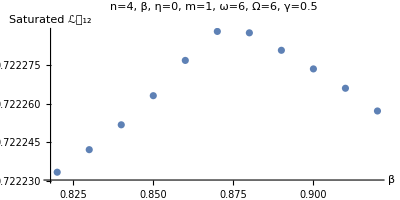
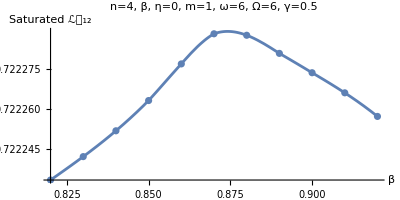

```mathematica
(* Plot only Points of where suspected Max is *)
MeanBetaDataptPlotZoom=ListPlot[MeanBetaData, Joined->False, Evaluate[PlotFormat1], Evaluate[LabelingInfo1]];
(* Interpolation: Must zoom in to where the suspected maximum is. *)
iMeanBetafunc=Interpolation[MeanBetaData]
iMeanBetaDatalinePlot=Plot[iMeanBetafunc[x], {x, 0.82, 0.92}, Evaluate[PlotFormat1], Evaluate[LabelingInfo1]];
(* Show together *)
Row[{MeanBetaDataptPlotZoom, Show[iMeanBetaDatalinePlot, MeanBetaDataptPlotZoom]}]
```

```mathematica
(* Take the derivative of the Interpolation Function *)
derivfunc[β_]:=D[iMeanBetafunc[x], x]/.x->β
(* Calculating the value of the derivative of Interpolation Function near the maximum. Get start and end values from the graph. *)
start= 0.869;
end=0.880;
deridata=Table[{β, derivfunc[β]}, {β, start, end, 10^-6}];
```

{0.874156,0.722289}

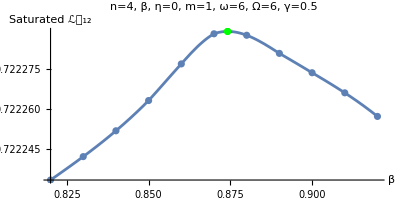

```mathematica
(* Finding Optimum β for when Ω=ω=6 *)
βmax={};
Table[If[deridata[[value]][[2]]>0 && deridata[[value+1]][[2]]<0, AppendTo[βmax, Mean[{deridata[[value]][[1]],deridata[[value+1]][[1]]}]]], {value, 1, Length[deridata]-1}];
optimumpt=Flatten[{βmax, iMeanBetafunc[βmax]}]
(* Plot {βmax, Saturated LN12} *)
optimumptPlot=ListPlot[{optimumpt}, Joined->False, Evaluate[PlotFormat1], Evaluate[LabelingInfo1], PlotStyle->Green];
Show[iMeanBetaDatalinePlot, MeanBetaDataptPlotZoom, optimumptPlot]
```